## Lesson 17: Series solutions near an ordinary point

## Overview

This lesson explores how to use a Taylor series to solve differential equations.

When the coefficients of a linear second-order differential equation become polynomials, the equation appears in the form:

P(x) y''(x)+Q(x)y'(x)+R(x)y(x)=0

A Taylor series can be determined at a point.

When you substitute the Taylor series for y(x) in the equation, it will solve the equation at that particular point:

y(x)=∑_(n=0)^∞ (a_n(x-x_o))^n

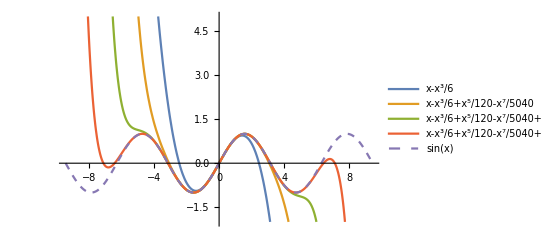

```mathematica
nsol[n_]:=AsymptoticDSolveValue[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,n}]
Plot[Evaluate[{nsol[4],nsol[8],nsol[12],nsol[16],Sin[x]}],{x,-3Pi,3Pi},]
```

## Methodology

Suppose y(x) is a function that solves the following differential equation:

P(x) y''(x)+Q(x)y'(x)+R(x)y(x)=0

For a fixed x_o with P(x_o)≠0, the point is called an ordinary point.

If x_o is an ordinary point, the equation can be rewritten as:

y''(x_o)=-p(x_o)y'(x_o)-q(x_o)y(x_o)

with p(x_0)=(Q(x_0))/(P(x_0)) and q(x_0)=(R(x_0))/(P(x_0)).

Recall that the coefficients of a Taylor series take the form:

a_n=(y^(n)(x_o))/(n!)

So it must be that:

2! a_2=-p(x_o)a_1-q(x_o)a_o

## Methodology

An expression for a_3 can be obtained by differentiating the entire equation:

```mathematica
D[y''[x]==-p[x]y'[x]-q[x]y[x],x]
```

y^(3)[x]==-y[x] q'[x]-q[x] y'[x]-p'[x] y'[x]-p[x] y''[x]

Replacing n!a_n=y^(n)(x_0)  and x_0→0, it follows that:

3! a_3=(-p y''+(-p'-q)y'-q'y )|_(x=x_o)

Using n!a_n=y^(n)(x_o) to replace the derivatives, it follows that:

3! a_3=(-2! p a_2-(p'+q)a_1-q' a_0)|_(x=x_o)

Because p and q are polynomials, this process can be continued indefinitely.

Ideally, you would like to obtain an expression for the general coefficient.

## Example 1

Determine a_2, a_3, a_4 about the point x_0=0 for the initial value problem:

2 y''(x)+(x+1)y'(x)+x^2 y(x)=0

y(0)=0

y'(0)=1

Begin by rewriting the equation in the form:

y''(x)=-(x+1)/2y'(x)-x^2/2 y(x)

Recall that the coefficients of a Taylor series take the form:

a_n=(y^(n)(x_o))/(n!)

From the initial conditions, it must be that:

a_0=0

a_1=1

## Example 1

In order to calculate a_2, a_3, a_4, use the equation:

2! a_2=-a_1/2 → a_2=-1/4

Differentiate the equation to obtain:

```mathematica
D[y''[x]==(-x-1)y'[x]/2-x^2 y[x]/2,x]
```

y^(3)[x]==-x y[x]-y'[x]/2-1/2 x^2 y'[x]+1/2 (-1-x) y''[x]

Replacing n!a_n=y^(n)(x_0) and x_0→0, it follows that:

3! a_3=-a_1/2-a_2→a_3=-1/24

## Example 1

Finally, for a_4, differentiate the equation twice to get:

```mathematica
D[y''[x]==(-x-1)y'[x]/2-x^2 y[x]/2,x,x]
```

y^(4)[x]==-y[x]-2 x y'[x]-y''[x]-1/2 x^2 y''[x]+1/2 (-1-x) y^(3)[x]

Replacing n!a_n=y^(n)(x_0) and x_0→0, it follows that:

a_4 =5/192

You can confirm the result that a_2=-1/4,a_3=-1/24, a_4=5/192 using the function AsymptoticDSolveValue:

```mathematica
AsymptoticDSolveValue[{2y''[x]+(1+x)y'[x]+x^2 y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,4}]
```

x-x^2/4-x^3/24+(5 x^4)/192

## Analytic Functions

When a function has a Taylor series representation that converges to the function at a point, the function is said to be analytic at that point.

For the differential equation:

P(x)y''(x)+Q(x)y'(x)+R(x)y(x)=0

when p=Q/P and q=R/P are analytic at x_0, the general solution of the differential equation is:

y(x)=∑_(n=0)^∞ (a_n(x-x_o))^n=a_0 y_1(x)+a_1 y_2(x)

where a_0 and a_1 are arbitrary constants and y_1(x) and y_2(x) are two power series solutions that are analytic at x_0.

These solutions form a fundamental solution set and the radius of convergence for each y_1(x) and y_2(x) is larger than or equal to the radii of convergence of the series for the functions p(x) and q(x).

## Example 2: Find a Solution

Find a series solution of the differential equation and determine the radius of convergence of this solution:

y''(x)+y(x)=0

y(0)=0

y'(0)=1

Begin by rewriting the equation in the form:

y''(x)=-y(x)

Recall that the coefficients of a Taylor series take the form:

a_n=(y^(n)(x_o))/(n!)

From the initial conditions it must be that:

a_0=0

a_1=1

## Example 2: Find a Solution

In order to calculate a_2, a_3, a_4, use the differential equation:

2! a_2=-a_0→a_2=0

Differentiate the equation to obtain:

```mathematica
D[y''[x]==-y[x],x]
```

y^(3)[x]==-y'[x]

Replacing n!a_n=y^(n)(x_0) and x_0→0, it follows that:

3! a_3=-(1!)a_1→a_3=-1/(3!)

For a_4:

4! a_4=-(2!)a_2→a_4=-(2!)/(4!)a_2

You can see a pattern beginning to develop where:

n!a_n=-(n-2)!a_(n-2)

## Example 2: Find a Solution

Identify a general expression for the n^th coefficient:

a_n=-((n-2)!)/(n!)a_(n-2)→a_n=-1/(n(n-1))a_(n-2)

You can solve for a_n using the function RSolveValue:

```mathematica
FullSimplify[RSolveValue[{a[n]==(-1/(n(n-1)))a[n-2],a[0]==0,a[1]==1},a[n],n]/.{n->2k+1},k∈Integers]
```

(-1)^k/Gamma[2+2 k]

Thus a_n=(-1)^k/((2k+1)!) when n=2k+1 and a_n=0 when n=2k.

Therefore, the series solution will be:

∑_(n=0)^∞ (-1)^n/((2n+1)!)x^(2n+1)

In order to determine the radius of convergence, you can use SumConvergence:

```mathematica
SumConvergence[(-1)^n/Factorial[2n+1] x^(2n+1),n]
```

True

When the output is True, the series will converge for any x value.

## Example 2: Find a Solution

Thus, the series solution is:

∑_(n=0)^∞ (-1)^n/((2n+1)!)x^(2n+1)

and this converges to the solution for any value of x.

This is a familiar form of a Taylor series for sin(x):

```mathematica
Sum[(-1)^n/Factorial[2n+1] x^(2n+1),{n,0,∞}]
```

Sin[x]

The series converges as you add more and more terms to the series.

To see this, first define the series up to n terms using AsymptoticDSolveValue:

```mathematica
nsol[n_]:=AsymptoticDSolveValue[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,n}]
```

Then plot the solution for different values of n:

```mathematica
Plot[Evaluate[{nsol[4],nsol[8],nsol[12],nsol[16],Sin[x]}],{x,-3Pi,3Pi},]
```

-Graphics-

## Example 3: Determine Convergence

Determine the radius of convergence of a series solution for this differential equation:

(x^2+1)y''(x)+y(x)=0

y(0)=0

y'(0)=1

Begin by rewriting the equation in the form:

y''(x)=-1/(1+x^2)y(x)

Identify p=0, q=-1/(1+x^2) and recall that the series solution converges wherever the functions p and q are analytic.

It is clear for p=0 it is analytic everywhere.

For q, examine the Taylor series using the function Series:

```mathematica
Series[-1/(1+x^2),{x,0,10}]
```

-1+x^2-x^4+x^6-x^8+x^10+O[x]^11

An obvious pattern is developing, which can be checked using Sum:

```mathematica
Sum[(-1)^(n+1) x^(2n),{n,0,∞}]
```

-1/(1+x^2)

Thus q has Taylor series ∑_(n=0)^∞ (-1)^(n+1)x^(2n).

## Example 3: Determine Convergence

To determine where q is analytic, you need to know for what values of x this series converges.

To determine the radius of convergence of this series, use SumConvergence:

```mathematica
SumConvergence[(-1)^(n+1) x^(2 n),n]
```

Abs[x]<1

Thus the radius of convergence of q is 1 and by extension, any series solution also has a radius of convergence at least 1:

```mathematica
nsol[n_]:=AsymptoticDSolveValue[{(x^2+1)y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],{x,0,n}]
```

After defining the series solution function, you can plot the solution for different values of n and compare with the result from DSolveValue:

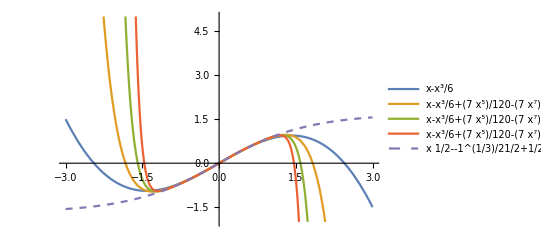

```mathematica
Plot[Evaluate[{nsol[4],nsol[8],nsol[12],nsol[16],DSolveValue[{(x^2+1)y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],x]}],{x,-3,3},]
```

You can observe quite clearly the convergence of the series solution in the interval (-1,1).

## Summary

When the coefficients of a linear second-order differential equation are polynomial functions of the independent variable x, the equation appears in the form:

P(x)y''(x)+Q(x)y'(x)+R(x)y(x)=0

You can determine a Taylor series solution at a point when p=Q/P and q=R/P are analytic at x_0:

y=∑_(n=0)^∞ (a_n(x-x_o))^n

Series solutions can be calculated in the Wolfram Language using AsymptoticDSolveValue.